```mathematica
(*natural constants*)
c:=3*10^10(*cm/s*)
qe:=1.6*10^-19(*C*)
Subscript[ϵ, 0]:=8.854*10^-12(*F m^-1*)
(*plasma*)
Subscript[n, p]:=5.0*10^16
Subscript[ω, p]:=5.64*10^4 √Subscript[n, p](*rad/s*)
Subscript[k, p]:=Subscript[ω, p]/c(*cm^-1*)
Subscript[λ, p]:=2π/Subscript[k, p](*cm*)
Subscript[λ, β]:=Subscript[λ, p] √(2γ)(*cm*)
Subscript[k, β]:=2 π / Subscript[λ, β](*cm^-1*)
Subscript[ω, β]:=c Subscript[k, β](*rad/s*)
Text["λ_p/2 (µm):"]
10^4*Subscript[λ, p]/2
(*e-beam*)
γ:=40000
β:=(1-1/γ^2)^(1/2)
Subscript[σ, r]:=30*10^-6(*m*)
Subscript[σ, z]:=30*10^-6(*m*)
Subscript[N, tot]:=0.7*10^10(*elec.*)
Subscript[Q, tot]:=Subscript[N, tot]*qe(*C*)
Λ:=(Subscript[Q, tot] c/100)/(√(2π Subscript[σ, z]^2))
Text["Λ (kA):"]
Λ/10^3
(*laser*)
ax:=1.5(*deg*)
n:=1.37397
Subscript[α, 0]:=ax(n-1)*π/180 (*rad*)
λ:=800.*10^-9(*m*)
Subscript[E, laser]:=500*10^-3(*J*)
Subscript[τ, laser]:=100*10^-15(*s*)
Subscript[z, min]:=0.5(*m*)
Subscript[r, mask]:=Subscript[z, min] Subscript[α, 0](*m*)
Subscript[z, max]:=5.0(*m*)
Subscript[w, 0]:=Subscript[z, max] Subscript[α, 0](*m*)
k:=2 π / λ(*m^-1*)
Subscript[ϕ, ax]:=(Subscript[E, laser]*10^3)/(π Subscript[w, 0]^2*10^4)(*mJ/cm^2*)
Text["mask radius (mm):"]
Subscript[r, mask]*10^3
Text["laser diameter (mm):"]
2 Subscript[w, 0]*10^3
Text["Energy flux on axicon (mJ/cm^2):"]
Subscript[ϕ, ax]
```

λ_p/2 (µm):

74.7321

Λ (kA):

4.46815

mask radius (mm):

4.89526

laser diameter (mm):

97.9051

Energy flux on axicon (mJ/cm^2):

6.64155

```mathematica
(*peak current and blowout radius calculations*)
(*see Wei Lu's paper Physics of Plasmas 2006*)
Subscript[R, b]=2.58 (Λ/(qe c)1/Subscript[n, p])^(1/2)(*cm*);(*use ';' and not ':='*)
Text["R_b (µm):"]
10^4*Subscript[R, b]
Subscript[RR, b][nn_]:=2.58 (Λ/(qe c))^(1/2)nn^(-1/2)
Plot[Subscript[RR, b][nn]/10^-4,{nn,1*10^16,5*10^16},AxesLabel->{"n_p (cm^-3)","R_b (µm)"}]
```

R_b (µm):

111.321

-Graphics-

E_r[2σ_r] (GV/m):

2.23103

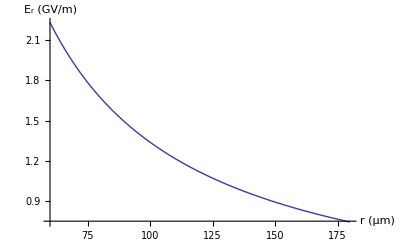

```mathematica
Subscript[E, r][rr_]:=1/(4π Subscript[ϵ, 0])Λ/(rr c/100)
Text["E_r[2σ_r] (GV/m):"]
Subscript[E, r][2 Subscript[σ, r]]/10^9
Plot[Subscript[E, r][rr*10^-6]/10^9,{rr,2 Subscript[σ, r]/10^-6,6 Subscript[σ, r]/10^-6},AxesLabel->{"r (µm)","E_r (GV/m)"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Field strength for 100% ionization in H for e-beam (GV/m):

27.0537

Field strength for 100% ionization in He for e-beam (GV/m):

72.6195

Field strength for 100% ionization in Li for e-beam (GV/m):

5.33414

Field strength for 100% ionization in Ar for e-beam (GV/m):

34.9035

Field strength for 100% ionization in Ar2 for e-beam (GV/m):

60.0775

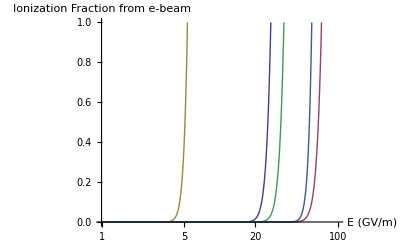

-Graphics-

```mathematica
(*Field ionization calculations*)
(*see Weiming An's paper from AAC2010*)
Subscript[n, eff][ZZ_,ξξ_]:=3.69 ZZ / ξξ^(1/2)
(*Hydrogen*)
Subscript[Z, H] := 1
Subscript[ξ, iH]:=13.6(*eV*)
Subscript[n, effH]:=Subscript[n, eff][Subscript[Z, H],Subscript[ξ, iH]]
(*Helium*)
Subscript[Z, He] := 1
Subscript[ξ, iHe]:=24.5(*eV*)
Subscript[n, effHe]:=Subscript[n, eff][Subscript[Z, He],Subscript[ξ, iHe]]
(*Lithium*)
Subscript[Z, Li]:=1
Subscript[ξ, iLi]:=5.39(*eV*)
Subscript[n, effLi]:=Subscript[n, eff][Subscript[Z, Li],Subscript[ξ, iLi]]
(*Argon*)
Subscript[Z, Ar]:=1
Subscript[ξ, iAr]:=15.8(*eV*)
Subscript[n, effAr]:=Subscript[n, eff][Subscript[Z, Ar],Subscript[ξ, iAr]]
(*Argon2*)
Subscript[Z, Ar2]:=2
Subscript[ξ, iAr2]:=27.6(*eV*)
Subscript[n, effAr2]:=Subscript[n, eff][Subscript[Z, Ar2],Subscript[ξ, iAr2]]
EE0=Subscript[E, r][2.5 Subscript[σ, r]]/10^9(*GV/m*);
Subscript[Δt, ebeam]:=Subscript[σ, z]/(c/100)
Subscript[Δt, laser]:=Subscript[τ, laser]
w[nn_,ξξ_,EE_]:=1.52*10^15(4^nn ξξ)/(nn Gamma[2 nn])((20.5 ξξ^(3/2))/EE)^(2nn-1)ⅇ^(-(6.83 ξξ^(3/2))/EE)(*s^-1*)
wH[EE_]:=w[Subscript[n, effH],Subscript[ξ, iH],EE](*s^-1*)
wHe[EE_]:=w[Subscript[n, effHe],Subscript[ξ, iHe],EE](*s^-1*)
wLi[EE_]:=w[Subscript[n, effLi],Subscript[ξ, iLi],EE](*s^-1*)
wAr[EE_]:=w[Subscript[n, effAr],Subscript[ξ, iAr],EE](*s^-1*)
wAr2[EE_]:=w[Subscript[n, effAr2],Subscript[ξ, iAr2],EE](*s^-1*)
Subscript[E, critH]=Solve[{wH[EE]*Subscript[Δt, ebeam]==1,EE>0,EE<100},EE][[1]][[1]][[2]]*10^9(*V/m*);
Subscript[E, critHe]=Solve[{wHe[EE]*Subscript[Δt, ebeam]==1,EE>0,EE<100},EE][[1]][[1]][[2]]*10^9(*V/m*);
Subscript[E, critLi]=Solve[{wLi[EE]*Subscript[Δt, ebeam]==1,EE>0,EE<100},EE][[1]][[1]][[2]]*10^9(*V/m*);
Subscript[E, critAr]=Solve[{wAr[EE]*Subscript[Δt, ebeam]==1,EE>0,EE<100},EE][[1]][[1]][[2]]*10^9(*V/m*);
Subscript[E, critAr2]=Solve[{wAr2[EE]*Subscript[Δt, ebeam]==1,EE>0,EE<100},EE][[1]][[1]][[2]]*10^9(*V/m*);
Text["Field strength for 100% ionization in H for e-beam (GV/m):"]
Subscript[E, critH]/10^9
Text["Field strength for 100% ionization in He for e-beam (GV/m):"]
Subscript[E, critHe]/10^9
Text["Field strength for 100% ionization in Li for e-beam (GV/m):"]
Subscript[E, critLi]/10^9
Text["Field strength for 100% ionization in Ar for e-beam (GV/m):"]
Subscript[E, critAr]/10^9
Text["Field strength for 100% ionization in Ar2 for e-beam (GV/m):"]
Subscript[E, critAr2]/10^9
LogLinearPlot[{wH[EE]*Subscript[Δt, ebeam],wHe[EE]*Subscript[Δt, ebeam] ,wLi[EE]*Subscript[Δt, ebeam],wAr[EE]*Subscript[Δt, ebeam],wAr2[EE]*Subscript[Δt, ebeam]},{EE,1,100},AxesLabel->{"E (GV/m)","Ionization Fraction from e-beam"},PlotRange->1]
LogLinearPlot[{wH[EE]*Subscript[Δt, laser],wHe[EE]*Subscript[Δt, laser] ,wLi[EE]*Subscript[Δt, laser],wAr[EE]*Subscript[Δt, ebeam],wAr2[EE]*Subscript[Δt, ebeam]},{EE,1,100},AxesLabel->{"E (GV/m)","Ionization Fraction from e-beam"},PlotRange->1]
```

Critical Intensity for 100% ionization of H (W/cm^2):

9.72043×10^13

Critical Intensity for 100% ionization of He (W/cm^2):

7.00386×10^14

Critical Intensity for 100% ionization of Li (W/cm^2):

3.77884×10^12

Critical Intensity for 100% ionization of Ar (W/cm^2):

1.61796×10^14

Critical Intensity for 100% ionization of Ar2 (W/cm^2):

4.79352×10^14

I_0 (W/cm^2):

6.24306×10^6

ρ_0 (µm):

31.2771

r_p[z_max] (µm):

Solve::nint: Warning: Solve used numeric integration to show that the solution set found is complete.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

1000000 {}⟦2⟧

z_start

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

{}⟦2⟧

Intensity as a function of radius and distance

-Graphics3D-

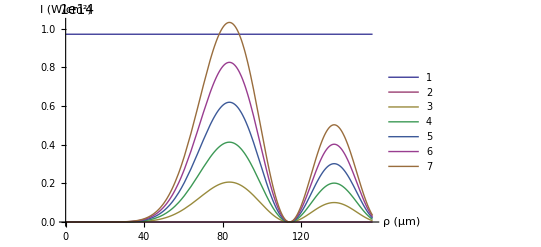

```mathematica
(*Laser ionization calculations*)
(*see Brzobohaty's paper Opics Express 2008*)
(*see Cizmar's PhD Thesis 2006*)
Subscript[I, critH]:=(Subscript[ϵ, 0] c/100)/2 Subscript[E, critH]^2*10^-4(*W/cm^2*)(*flat top*)
Subscript[I, critHe]:=(Subscript[ϵ, 0] c/100)/2 Subscript[E, critHe]^2*10^-4(*W/cm^2*)(*flat top*)
Subscript[I, critLi]:=(Subscript[ϵ, 0] c/100)/2 Subscript[E, critLi]^2*10^-4(*W/cm^2*)(*flat top*)
Subscript[I, critAr]:=(Subscript[ϵ, 0] c/100)/2 Subscript[E, critAr]^2*10^-4(*W/cm^2*)(*flat top*)
Subscript[I, critAr2]:=(Subscript[ϵ, 0] c/100)/2 Subscript[E, critAr2]^2*10^-4(*W/cm^2*)(*flat top*)
Text["Critical Intensity for 100% ionization of H (W/cm^2):"]
Subscript[I, critH]
Text["Critical Intensity for 100% ionization of He (W/cm^2):"]
Subscript[I, critHe]
Text["Critical Intensity for 100% ionization of Li (W/cm^2):"]
Subscript[I, critLi]
Text["Critical Intensity for 100% ionization of Ar (W/cm^2):"]
Subscript[I, critAr]
Text["Critical Intensity for 100% ionization of Ar2 (W/cm^2):"]
Subscript[I, critAr2]
Subscript[I, f0]:=0.94 Subscript[E, laser]/(Subscript[τ, laser] π Subscript[w, 0]^2)*10^-4(*W/cm^2*)(*flat top*)
Subscript[I, g0]:=1.88 Subscript[E, laser]/(Subscript[τ, laser] π Subscript[w, 0]^2)*10^-4(*W/cm^2*)(*gaussian*)
Text["I_0 (W/cm^2):"]
Subscript[I, f0]*10^-4
Subscript[ρ, 0]:=2.405/(k Sin[Subscript[α, 0]])(*m*)
Text["ρ_0 (µm):"]
Subscript[ρ, 0]*10^6
IIf[ρρ_,zz_]:=Subscript[I, f0] 2π k Sin[Subscript[α, 0]]^2 zz BesselJ[5,k ρρ Sin[Subscript[α, 0]]]^2(*W/cm^2*)(*flat top*)
IIg[ρρ_,zz_]:=Subscript[I, g0] 2π k Sin[Subscript[α, 0]]^2 zz BesselJ[0,k ρρ Sin[Subscript[α, 0]]]^2 Exp[-2 zz^2/Subscript[z, max]^2](*W/cm^2*)(*gaussian*)
Subscript[R, ion][zz_]:=Solve[IIf[ρρ,zz]==Subscript[I, critH]&& ρρ>0 && ρρ<Subscript[ρ, 0],ρρ][[1]][[1]][[2]]
Text["r_p[z_max] (µm):"]
Subscript[R, ion][Subscript[z, max]]/10^-6
Text["z_start"]
Solve[IIf[0,zz]==Subscript[I, critH]&& zz>0 && zz<Subscript[z, max],zz][[1]][[1]][[2]]
Text["Intensity as a function of radius and distance"]
Plot3D[{IIf[ρρ*10^-6,zz],Subscript[I, crtiH]},{ρρ,0,250},{zz,0,Subscript[z, max]},AxesLabel->{"ρ (µm)","z (m)","I (W/cm^2)"},PlotRange->{0,1.0*Subscript[I, critH]},Mesh->{25-1,10-1},MeshStyle->Black,PerformanceGoal->"Quality"]
Plot[{Subscript[I, critH],IIf[ρρ*10^-6,0.0],IIf[ρρ*10^-6,0.5],IIf[ρρ*10^-6,1.0],IIf[ρρ*10^-6,1.5],IIf[ρρ*10^-6,2.0],IIf[ρρ*10^-6,2.5]},{ρρ,0,5*Subscript[ρ, 0]/10^-6},AxesLabel->{"ρ (µm)","I (W/cm^2)"},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
Text["Maximum radius at which intensity exceeds H ionization threshold as a function of z"]
Plot[{Subscript[R, ion][zz]/10^-6,2.5*Subscript[σ, r]/10^-6,Subscript[R, b]/10^-4},{zz,0.0,Subscript[z, max]},AxesLabel->{"z (m)","ρ (µm)"},PlotRange->{0,1.1*Subscript[R, b]/10^-4}]
```

Maximum radius at which intensity exceeds H ionization threshold as a function of z

Solve::nint: Warning: Solve used numeric integration to show that the solution set found is complete.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Solve::nint: Warning: Solve used numeric integration to show that the solution set found is complete.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Plot::prng: Value of option PlotRange -> {0, 2.73814×10^10\ √1/1.37397`_p} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

$Aborted